```mathematica
(*Константы*)

L1=SetPrecision[ 13.2698866354446, 15]; L2=SetPrecision[0.546803420570484, 15];

C1=SetPrecision[0.0000113340568414556, 15];C2=SetPrecision[0.0000104824764853959, 15];

R1=SetPrecision[104.343183349745, 15]; R2=SetPrecision[38.2349827013823, 15];
R3=SetPrecision[1058.10097746217, 15];R4=SetPrecision[523.621273361832, 15];

dt=SetPrecision[0.0196349540849362, 15];
N1=8192;
t = dt * N1;
```

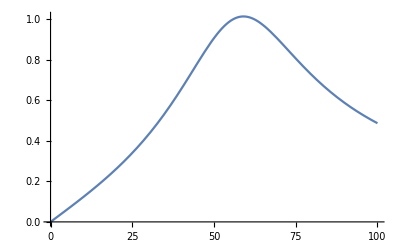

```mathematica
Z1[w_] = R4 + 1/(I w C2); 
Z2[w_]= R3+R2 + I w L2 + 1/(I w C1); 
Ztotal[w_] =(1/Z1[w]+1/Z2[w])^-1; (*общий*)
I1[w_] = Uin/(R1 + I w L1 + Ztotal[w]);
Utotal[w_] = I1[w] * Ztotal[w];
I2[w_] = Utotal[w]/Z2[w];
Uout[w_] = I2[w] * R3;

H[w_]= Uout[w]/Uin;

Plot[Abs@H[w],{w, 0, 100}]
```

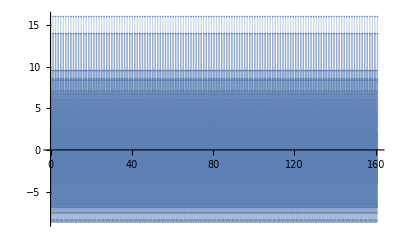

```mathematica
file = ReadList["C:\\foit\\IDZ3\\6.txt"];
table=Table[{(i-1)*dt, file[[i]]},{i,1,N1}];
ListPlot[table, Filling->Axis,PlotRange->Full]
```

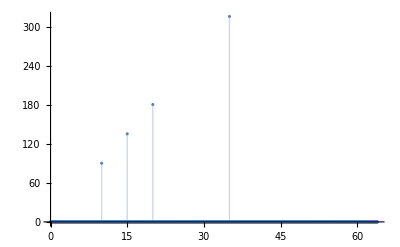

```mathematica
F=Fourier[file];
Nf=Length@F;
df=1/t;
Ftable=Table[{2π df (i-1), Abs@F[[i]]},{i,1,Nf/5}];
ListPlot[Ftable, Filling->Axis,PlotRange->Full]
```

0.2596833455775

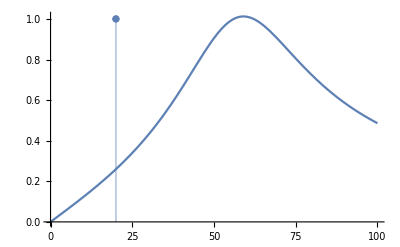

```mathematica
Abs@H[20]
Show[Plot[Abs@H[w],{w, 0, 100}], ListPlot[{{20, 1}}, Filling->Axis]]
```